Badges indicate graded exercises for certification

Make a list of the first 10 squares, in reverse order.

Expected Output »

{100,81,64,49,36,25,16,9,4,1}

```mathematica
Reverse[Range[10]^2]
```

{100,81,64,49,36,25,16,9,4,1}

Find the total of the first 10 squares.

Expected Output »

385

```mathematica
Total[Range[10]^2]
```

385

Make a plot of the first 10 squares, starting at 1.

Expected Output »

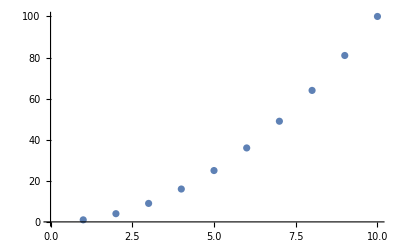

```mathematica
ListPlot[Range[10]^2]
```

-Graphics-

Make a list of the first 10 multiples of 3.

Expected Output »

{3,6,9,12,15,18,21,24,27,30}

```mathematica
Range[10]*3
```

{{3,6,9,12,15,18,21,24,27,30}}

Use Sort, Join and Range to create {1,1,2,2,3,3,4,4,}.

Expected Output »

{1,1,2,2,3,3,4,4}

```mathematica
Sort[Join[Range[4], Range[4]]]
```

{1,1,2,2,3,3,4,4}

Use Range and + to make a list of numbers from 10 to 20, inclusive.

Expected Output »

{10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Range[10,20]
```

{10,11,12,13,14,15,16,17,18,19,20}

Make a list of the first 10 squares using only Range and Times.

Expected Output »

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Times[Range[10]^2]
```

{1,4,9,16,25,36,49,64,81,100}

Make a combined list of the first 5 squares and cubes (numbers raised to the power 3), sorted into order.

Expected Output »

{1,1,4,8,9,16,25,27,64,125}

```mathematica
Sort[Join[{1,2,3,4,5}^2,  {1,2,3,4,5}^3]]
```

{1,1,4,8,9,16,25,27,64,125}

Find the number of digits in 2^128.

Expected Output »

39

```mathematica
IntegerLength[2^128]
```

39

Find the first digit of 2^32.

Expected Output »

4

IntegerDigits[2^32][[1]]

4

Find the first 10 digits in 2^100.

Expected Output »

{1,2,6,7,6,5,0,6,0,0}

```mathematica
Take[IntegerDigits[2^100],10]
```

{1,2,6,7,6,5,0,6,0,0}

Find the last digit of 2^37.

Expected Output »

2

```mathematica
Last[IntegerDigits[2^37]]
```

2

Find the second-to-last digit of 2^32.

Expected Output »

9

```mathematica
IntegerDigits[2^32][[-2]]
```

9

Find the largest digit that appears in 2^20.

Expected Output »

8

```mathematica
Max[IntegerDigits[2^20]]
```

8

Find the sum of all the digits of 3^126.

Expected Output »

234

```mathematica
Total[IntegerDigits[3^126]]
```

234

Find how many zeros appear in the digits of 2^1000.

Expected Output »

28

```mathematica
Count[IntegerDigits[2^1000],0]
```

28

Use Part, Sort and IntegerDigits to find the second-smallest digit in 2^20.

Expected Output »

1

```mathematica
Part[Sort[IntegerDigits[2^20]],2]
```

1

Make a line plot of the sequence of digits that appear in 2^128

Expected Output »

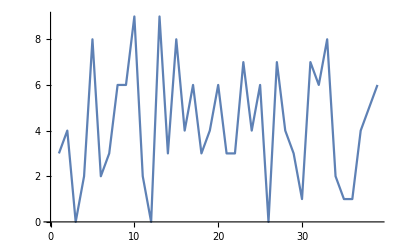

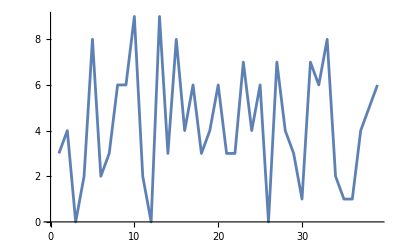

```mathematica
ListLinePlot[Transpose[{Range[Length[IntegerDigits[2^128]]],IntegerDigits[2^128]}]]
```

Make a pie chart of the sequence of digits that appear in 2^32.

Expected Output »

-Graphics-

```mathematica
PieChart[Tally[IntegerDigits[2^32]]]
```

-Graphics-

Make a list of pie charts for the sequence of digits in 2^20, 2^40, 2^60.

Expected Output »

{-Graphics-,-Graphics-,-Graphics-}

{1,1,0,0,1,1,1,1,1,0}

Use Take and Drop to get the sequence 11 through 20 from

Range[100]

Expected Output »

{11,12,13,14,15,16,17,18,19,20}

```mathematica
Take[Drop[Range[100], 10], 10]
```

{11,12,13,14,15,16,17,18,19,20}